```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<IsingScalingFunction`
```

## Checking Convergence

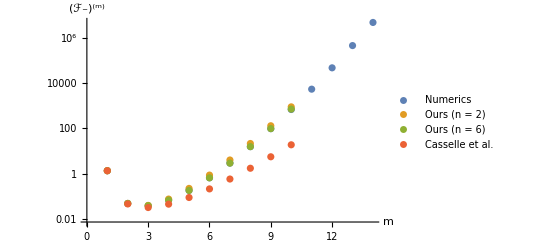

```mathematica
ListLogPlot[Abs@{
Rest@Gls,
Rest@(DScriptFPlusMinusDξθ0List@@PrepareArgument[Data[2]])[10],
Rest@(DScriptFPlusMinusDξθ0List@@PrepareArgument[Data[6]])[10],
DScriptMCasDξList[9,θ0Cas]Table[((m-1)!)/(m!),{m,1,10}]
},
PlotLegends->{"Numerics","Ours (n = 2)", "Ours (n = 6)", "Casselle et al."},
AxesLabel->{m,"(ℱ_-)^(m)"}
]
```

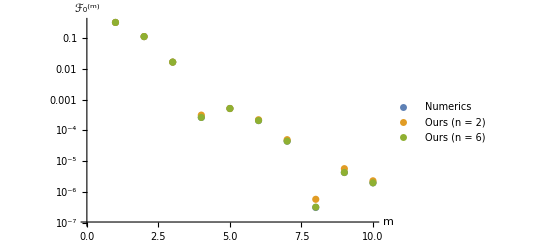

```mathematica
ListLogPlot[Abs@{
Rest@Φs,
Rest@(DScriptF0DηList@@PrepareArgument[Data[2]])[10,1],
Rest@(DScriptF0DηList@@PrepareArgument[Data[6]])[10,1]
},
PlotLegends->{"Numerics","Ours (n = 2)", "Ours (n = 6)"},
AxesLabel->{m,"ℱ_0^(m)"}
]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(371382927287350339456845128427992 «4» (-1+ⅇ^((«1»)/(«1»)) ExpIntegralEi[«1»]-(114355882310899360521914666542829 (114«10»4503)^(7/8) ⅇ^(«1») π ExpIntegralEi[-(«1»)/(«1»)])/(107668955486287134775550584515499446643328 2^(1/12) 189336221^(3/4) Glaisher^(3/2))))/(1075985451139697449885706090335689 189336221^(1/4) π^2)-(371382927287350339456845128427992 «4» (1-ⅇ^((«1»)/(«1»)) ExpIntegralEi[-(«1»)/(«1»)]+(«1»)/(«1»)))/(1075985451139697449885706090335689 189336221^(1/4) π^2).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -(46681463692889041973700532620906696296885587180818594561 (-(371382927287350339456845128427992 «4» (-1+ⅇ^Times[«1»] «13»[«1»]-(«1»)/(«1»)))/(1075985451139697449885706090335689 189336221^(1/4) π^2)-(«1»)/(«1»)))/383435814415399100830298627422256492275580379991986176+(1995291215029551557786949 (-(«1»)/(«1»)-(«1»)/(«1»)+12 (-(«1»)/(«1»)-(«1»)/(«1»))))/104122350499534957937152.

General::stop: Further output of N::meprec will be suppressed during this calculation.

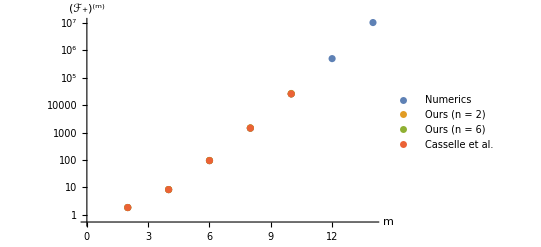

```mathematica
ListLogPlot[Abs@{
Rest@Ghs,
Rest@(DScriptFPlusMinusDξList@@PrepareArgument[Data[2]])[10,0],
Rest@(DScriptFPlusMinusDξList@@PrepareArgument[Data[6]])[10,0],
DScriptMCasDξList[9,0]Table[((m-1)!)/(m!),{m,1,10}]
},
PlotLegends->{"Numerics","Ours (n = 2)", "Ours (n = 6)", "Casselle et al."},
AxesLabel->{m,"(ℱ_+)^(m)"}
]
```

```mathematica
freeEnergyData=Table[{ut[1,γ Data[n]["θ0"]](uh[Data[n]["θ0"],Data[n]["gs"]][1,γ Data[n]["θ0"]])^(-8/15),Re@(DScriptF0DηList@@PrepareArgument[Data[n]])[0,γ Data[n]["θ0"]][[1]]},{n,2,6},Evaluate@N[{γ,10^-4,1-10^-4,10^-4},30]];
```

```mathematica
freeEnergyDataInterpolation=Interpolation/@freeEnergyData;
```

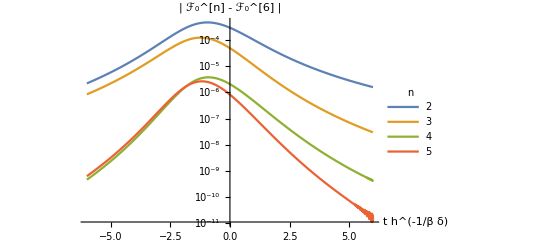

```mathematica
pCovergence=LogPlot[Evaluate[(Abs[#[x]-Last[freeEnergyDataInterpolation][x]])&/@Most[freeEnergyDataInterpolation]],{x,-6,6},PlotLegends->LineLegend[{2,3,4,5},LegendLabel->"n"],AxesLabel->{"t h^(-1/β δ)","| ℱ_0^[n] - ℱ_0^[6] |"},LabelStyle->{Black,FontSize->12}]
```

```mathematica
magnetizationData=Table[{ut[1,γ Data[n]["θ0"]](uh[Data[n]["θ0"],Data[n]["gs"]][1,γ Data[n]["θ0"]])^(-8/15),Re@(DScriptF0DηList@@PrepareArgument[Data[n]])[1,γ Data[n]["θ0"]][[-1]]},{n,2,6},Evaluate@N[{γ,10^-4,1-10^-4,10^-4},30]];
```

```mathematica
magnetizationDataInterpolation=Interpolation/@magnetizationData;
```

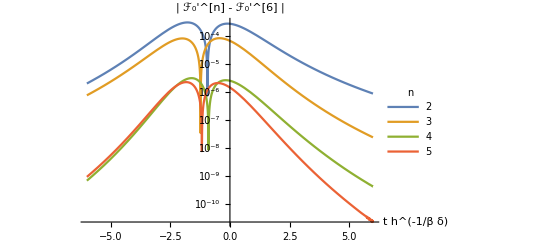

```mathematica
LogPlot[Evaluate[(Abs[#[x]-Last[magnetizationDataInterpolation][x]])&/@Most[magnetizationDataInterpolation]],{x,-6,6},PlotLegends->LineLegend[{2,3,4,5},LegendLabel->"n"],AxesLabel->{"t h^(-1/β δ)","| ℱ_0'^[n] - ℱ_0'^[6] |"},LabelStyle->{Black,FontSize->12}]
```

## Plotting as functions of scaling invariants

```mathematica
η2=η[Data[2]["θ0"],Data[2]["gs"]];
ξ2=ξ[Data[2]["θ0"],Data[2]["gs"]];
DScriptF0Dη2=DScriptF0Dη@@PrepareArgument[Data[2]];
η6=η[Data[6]["θ0"],Data[6]["gs"]];
ξ6=ξ[Data[6]["θ0"],Data[6]["gs"]];
DScriptF0Dη6=DScriptF0Dη@@PrepareArgument[Data[6]];
```

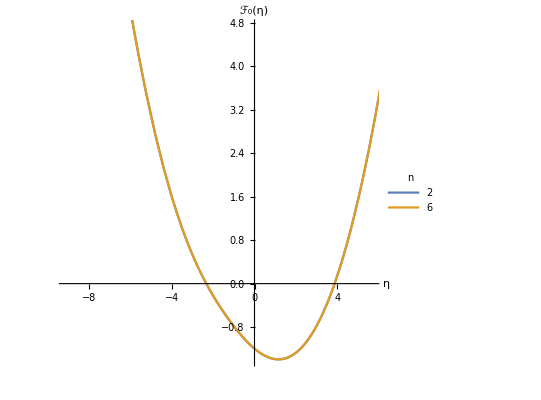

```mathematica
ParametricPlot[Evaluate@{
{η2[γ Data[2]["θ0"]],DScriptF0Dη2[0,γ Data[2]["θ0"]]},
{η6[γ Data[6]["θ0"]],DScriptF0Dη6[0,γ Data[6]["θ0"]]}
},{γ,0,0.999},
AspectRatio->1,AxesLabel->{η,Subscript[ℱ, 0][η]},LabelStyle->Black,PlotLegends->LineLegend[{2,6},LegendLabel->"n"]
]
```

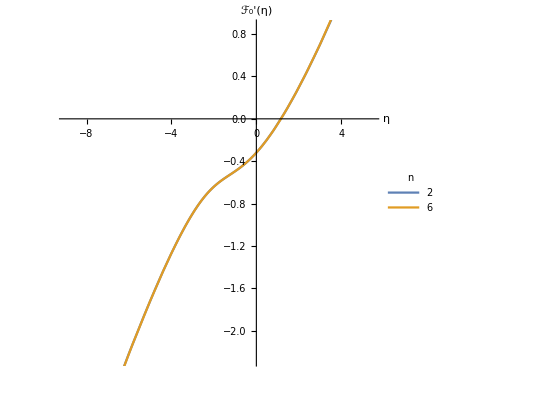

```mathematica
ParametricPlot[Evaluate@{
{η2[γ Data[2]["θ0"]],DScriptF0Dη2[1,γ Data[2]["θ0"]]},
{η6[γ Data[6]["θ0"]],DScriptF0Dη6[1,γ Data[6]["θ0"]]}
},{γ,0,0.999},
AspectRatio->1,AxesLabel->{η,Subscript[ℱ, 0]'[η]},LabelStyle->Black,PlotLegends->LineLegend[{2,6},LegendLabel->"n"]
]
```

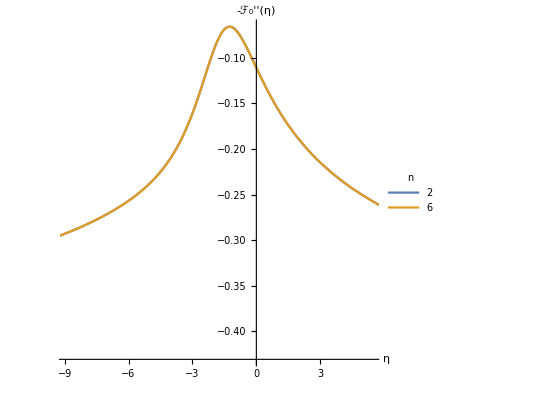

```mathematica
ParametricPlot[Evaluate@{
{η2[γ Data[2]["θ0"]],-DScriptF0Dη2[2,γ Data[2]["θ0"]]},
{η6[γ Data[6]["θ0"]],-DScriptF0Dη6[2,γ Data[6]["θ0"]]}
}
,{γ,0,0.999},
AspectRatio->1,AxesLabel->{η,-Subscript[ℱ, 0]''[η]},LabelStyle->Black,PlotLegends->LineLegend[{2,6},LegendLabel->"n"]
]
```

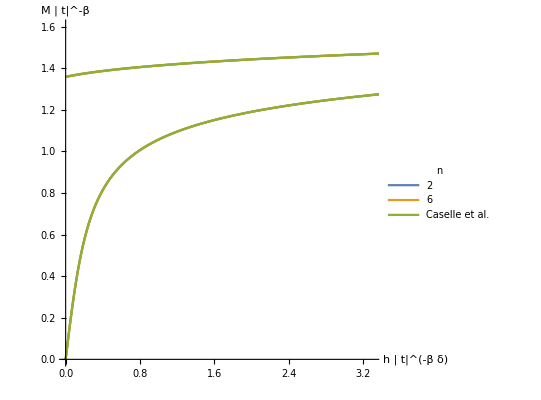

```mathematica
ParametricPlot[Evaluate@{
{ξ2[γ Data[2]["θ0"]],-(DufDuh@@PrepareArgument[Data[2]])[1][3,γ Data[2]["θ0"]] Abs[ut[3,γ Data[2]["θ0"]]]^(-1/8)},
{ξ6[γ Data[6]["θ0"]],-(DufDuh@@PrepareArgument[Data[6]])[1][3,γ Data[6]["θ0"]] Abs[ut[3,γ Data[6]["θ0"]]]^(-1/8)},
{ξ[θ0Cas,gsCas][γ θ0Cas],DScriptMCasDξList[0,γ θ0Cas][[-1]]}
},{γ,0,0.999},PlotRange->{{0,3.3},{0,1.6}},
AspectRatio->1,PlotPoints->50,AxesLabel->{"h | t|^(-β δ)","M | t|^-β"},LabelStyle->{Black,FontSize->14},PlotLegends->LineLegend[{2,6,"Caselle et al."},LegendLabel->"n"]
]
```

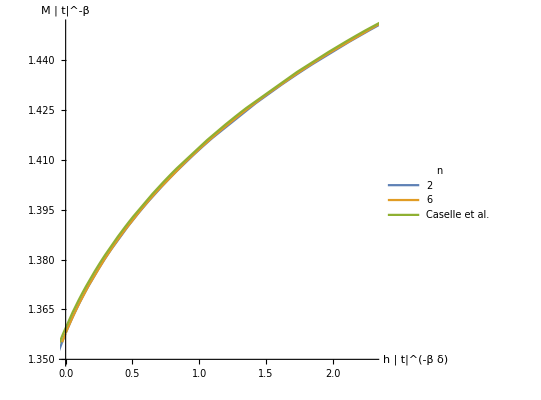

```mathematica
pMag=Show[ParametricPlot[Evaluate@{
{ξ[Data[2]["θ0"],Data[2]["gs"]][θ],-(DufDuh@@PrepareArgument[Data[2]])[1][1,θ] Abs[ut[1,θ]]^(-1/8)},
{ξ[Data[6]["θ0"],Data[6]["gs"]][θ],-(DufDuh@@PrepareArgument[Data[6]])[1][1,θ] Abs[ut[1,θ]]^(-1/8)},
{ξ[θ0Cas,gsCas][θ],DScriptMCasDξList[0,θ][[-1]]}
},{θ,0,1.4},
AspectRatio->1,PlotPoints->50,AxesLabel->{"h | t|^(-β δ)","M | t|^-β"},LabelStyle->{Black,FontSize->14},PlotRange->{{0,2.3},{1.35,1.45}},PlotLegends->LineLegend[{2,6,"Caselle et al."},LegendLabel->"n"]
]]
```

ParametricPlot::precw: The precision of the argument function ({((1-0.855059 θ^2) (0.272869 θ-0.060683 θ^3-0.0118826 θ^5-0.00404092 θ^7-0.00195592 θ^9))/(RealAbs[-1+θ^2]^(15/8)),0.+(-(0.251753 θ^2 (-1+θ^2))/RealAbs[Plus[«2»]]^(17/8)+1.00701/RealAbs[«1»]^(1/8))/(-(15 «3» (Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]))/(4 RealAbs[«1»]^(31/8))+((«1») («1»))/(«1»)^(15/8)-(«1»)/(«7»[«1»])^(15/8))}) is less than WorkingPrecision (20.).

ParametricPlot::precw: The precision of the argument function ({(-(15 θ (1-0.855059 θ^2) (-1+θ^2) (0.272869 θ-0.060683 θ^3-0.0118826 θ^5-0.00404092 θ^7-0.00195592 θ^9))/(4 RealAbs[-1+Power[«2»]]^(31/8))+((1-0.855059 θ^2) (0.272869-«20» θ^2-«1»-«20» «1»-0.0176033 θ^8))/RealAbs[-1+Power[«2»]]^(15/8)-(1.71012 θ («1»))/RealAbs[-1+Power[«2»]]^(15/8))-0,(-1+θ^2)-0,(1-θ^2)-0}) is less than WorkingPrecision (20.).

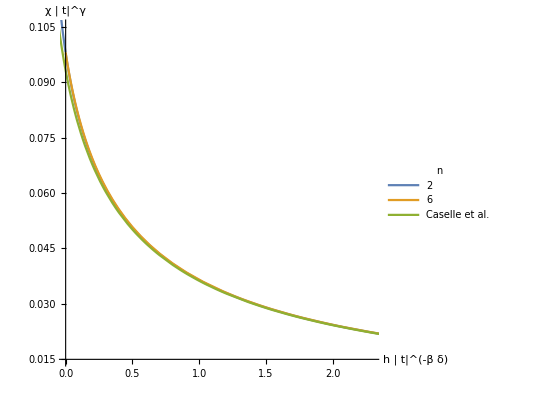

```mathematica
ParametricPlot[Evaluate@{
{ξ2[θ],-(DufDuh@@PrepareArgument[Data[2]])[2][1,θ] Abs[ut[1,θ]]^(7/4)},
{ξ6[θ],-(DufDuh@@PrepareArgument[Data[6]])[2][1,θ] Abs[ut[1,θ]]^(7/4)},
{ξ[θ0Cas,gsCas][θ],DScriptMCasDξList[1,θ][[-1]]}
},{θ,1,Data[6]["θ0"]},PlotRange->{{0,2.3},{0.015,0.105}},
AspectRatio->1,WorkingPrecision->20,PlotPoints->50,AxesLabel->{"h | t|^(-β δ)","χ | t|^γ"},LabelStyle->{Black,FontSize->14},PlotLegends->LineLegend[{2,6,"Caselle et al."},LegendLabel->"n"]
]
```

ParametricPlot::precw: The precision of the argument function ({((1-1. γ^2) (0.295091 γ-0.0767491 γ^3-0.0175761 γ^5-0.00699026 γ^7-0.00395703 γ^9))/(RealAbs[-1+1.16951 γ^2]^(15/8)),0.+(-(0.294427 «1» (-1+1.16951 Power[«1»]))/RealAbs[Plus[«2»]]^(17/8)+1.00701/(«7»[«1»])^(1/8))/(-(4.0554 γ (1+Times[«2»]) (-1+Times[«2»]) («1»))/RealAbs[«1»]^(31/8)+((1+Times[«2»])«1»(«1»«1»)/(«7»[«1»])^(15/8)-(«1»)/(«1»)^(15/8))}) is less than WorkingPrecision (20.).

ParametricPlot::precw: The precision of the argument function ({(-(4.0554 γ (1-1. γ^2) (-1+1.16951 γ^2) (0.295091 γ-0.0767491 γ^3-0.0175761 γ^5-0.00699026 γ^7-0.00395703 γ^9))/RealAbs[-1+Times[«2»]]^(31/8)+((1-1. γ^2) («1»))/RealAbs[-1+«1»]^(15/8)-(1.84939 γ (0.295091 γ-0.0767491 γ^3-«21» «1»-«22» γ^7-0.00395703 γ^9))/RealAbs[-1+Times[«2»]]^(15/8))-0,(-1+1.16951 «1»)-0,(1-1.16951 γ^2)-0}) is less than WorkingPrecision (20.).

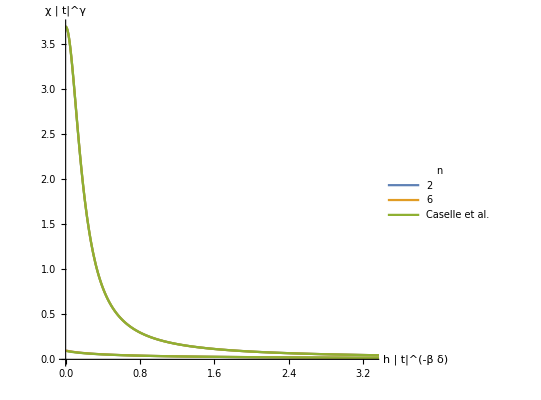

```mathematica
ParametricPlot[Evaluate@{
{ξ2[γ Data[2]["θ0"]],-(DufDuh@@PrepareArgument[Data[2]])[2][1,γ Data[2]["θ0"]] Abs[ut[1,γ Data[2]["θ0"]]]^(7/4)},
{ξ6[γ Data[6]["θ0"]],-(DufDuh@@PrepareArgument[Data[6]])[2][1,γ Data[6]["θ0"]] Abs[ut[1,γ Data[6]["θ0"]]]^(7/4)},
{ξ[θ0Cas,gsCas][γ θ0Cas],DScriptMCasDξList[1,γ θ0Cas][[-1]]}
},{γ,0,0.999},PlotRange->{{0,3.3},Automatic},
AspectRatio->1,WorkingPrecision->20,PlotPoints->50,AxesLabel->{"h | t|^(-β δ)","χ | t|^γ"},LabelStyle->{Black,FontSize->14},PlotLegends->LineLegend[{2,6,"Caselle et al."},LegendLabel->"n"]
]
```

## Plotting as functions of control variables

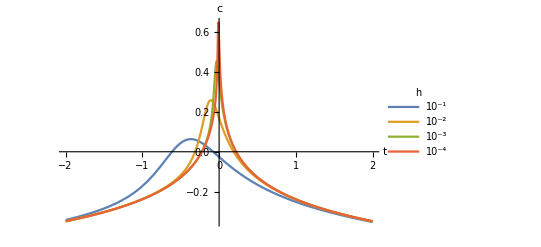

```mathematica
Plot[{
-Re[Evaluate[DufDut@@PrepareArgument[Data[6]]][2]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][t,10^-1]],
-Re[Evaluate[DufDut@@PrepareArgument[Data[6]]][2]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][t,10^-2]],
-Re[Evaluate[DufDut@@PrepareArgument[Data[6]]][2]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][t,10^-3]],
-Re[Evaluate[DufDut@@PrepareArgument[Data[6]]][2]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][t,10^-4]]
},{t,-2,2},PlotRange->All,Exclusions->None,AxesLabel->{t,"c"},LabelStyle->Black,PlotLegends->LineLegend[{"10^-1","10^-2","10^-3","10^-4"},LegendLabel->h]]
```

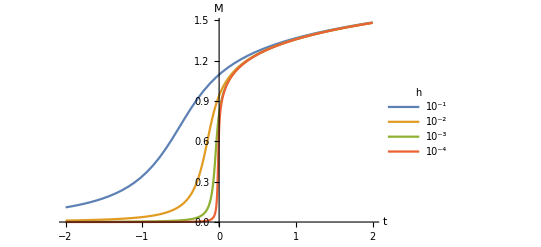

```mathematica
Plot[{
-Re[Evaluate[DufDuh@@PrepareArgument[Data[6]]][1]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][t,10^-1]],
-Re[Evaluate[DufDuh@@PrepareArgument[Data[6]]][1]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][t,10^-2]],
-Re[Evaluate[DufDuh@@PrepareArgument[Data[6]]][1]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][t,10^-3]],
-Re[Evaluate[DufDuh@@PrepareArgument[Data[6]]][1]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][t,10^-4]]
},{t,-2,2},PlotRange->All,Exclusions->None,AxesLabel->{t,"M"},LabelStyle->Black,PlotLegends->LineLegend[{"10^-1","10^-2","10^-3","10^-4"},LegendLabel->h]]
```

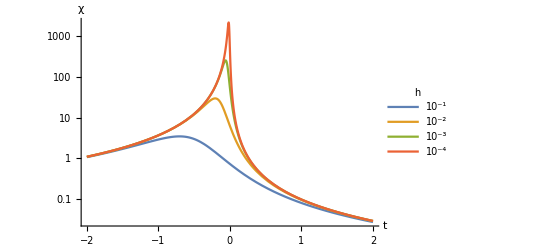

```mathematica
LogPlot[{
-Re[Evaluate[DufDuh@@PrepareArgument[Data[6]]][2]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][t,10^-1]],
-Re[Evaluate[DufDuh@@PrepareArgument[Data[6]]][2]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][t,10^-2]],
-Re[Evaluate[DufDuh@@PrepareArgument[Data[6]]][2]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][t,10^-3]],
-Re[Evaluate[DufDuh@@PrepareArgument[Data[6]]][2]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][t,10^-4]]
},{t,-2,2},Exclusions->None,PlotRange->All,AxesLabel->{t,"χ"},LabelStyle->Black,PlotLegends->LineLegend[{"10^-1","10^-2","10^-3","10^-4"},LegendLabel->h]]
```